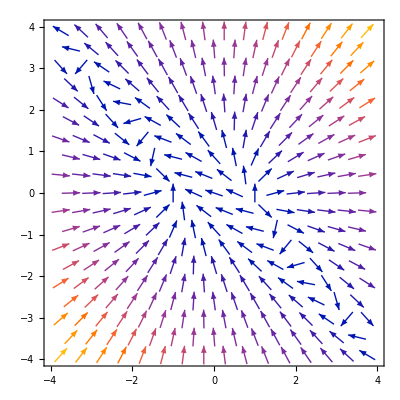

```mathematica
svl=γ/2-1/2 l(-3γ l - f);
svf=-1/2-1/2 f(-3γ l - f);
γ=1/3;
field=VectorPlot[{svf,svl},{f,-4,4},{l,-4,4}]
```

```mathematica
q1=Plot[y=√((-(1-x))/3),{x,-4,4},PlotStyle->Directive[Darker[Green,1],Thick]];
q2=Plot[y=-√((-(1-x))/3),{x,-4,4},PlotStyle->Directive[Darker[Green,1],Thick]];
q3=Plot[y=√((-(1+x))/3),{x,-4,4},PlotStyle->Directive[Darker[Green,1],Thick]];
q4=Plot[y=-√((-(1+x))/3),{x,-4,4},PlotStyle->Directive[Darker[Green,1],Thick]];
```

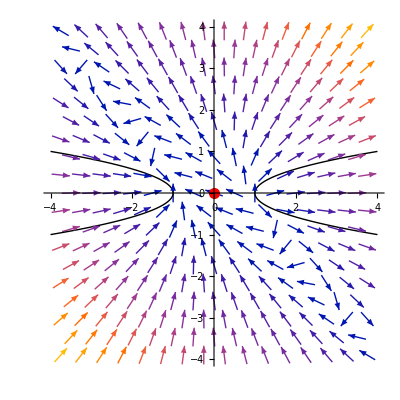

```mathematica
Show[phase1,field,q1,q2,q3,q4,PlotRange->{{-4,4},{-4,4}}]
```

```mathematica
ClearAll[f,l]
```

```mathematica
γ=1/3
```

1/3

```mathematica
eq1=f'[t]==-1/2-1/2 √(1/6)(-3γ l[t]-√(1/6));
eq2=l'[t]==γ/2-1/2 l[t](-3γ l[t]-√(1/6));
```

```mathematica
sol=NDSolve[{eq1,eq2,f[0]==√(1/6),l[0]==1},{l,f},{t,0,200}]
```

NDSolve::ndsz: At t == 1.56136, step size is effectively zero; singularity or stiff system suspected.

{{l→InterpolatingFunction[…],f→InterpolatingFunction[…]}}

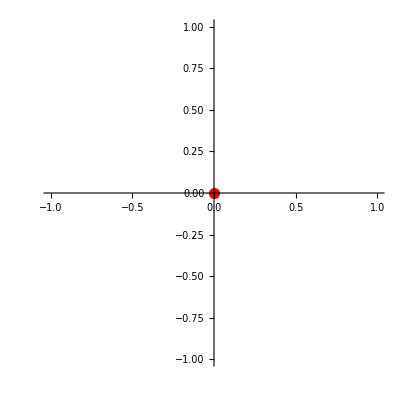

```mathematica
phase1=ParametricPlot[Evaluate[{f[x],l[x]}/.sol],{x,0,200},PlotStyle->Directive[Darker[Green,0.5],Thick],Epilog->{PointSize[0.02],Red,Point[{0,0}]},AspectRatio->1,PlotRange->All]
```